```mathematica
Differential Equations
```

### Slope Fields

In this lesson we learn about using Mathematica to investigate differential equations. One of the first graphical tools introduced in a class on differential equations are slope fields. Slope fields are easy for a computer to plot and can provide a lot of information about the nature of solutions as the initial conditions vary. A slope field can be thought of as a special case of a vector field (which you might remember from Math 241) and Mathematica can display vector fields using the built in function VectorPlot.

Consider the differential equation ⅆy/ⅆx= y - x.  To create the associated slope field, we wish to draw a small line at each point (x, y) having slope y - x. This can be accomplished in a few simple steps. First, we will create a vector field where we associate the vector ⟨1, y - x⟩ to each point (x, y). The following will show the vector field in an appropriate viewing window.

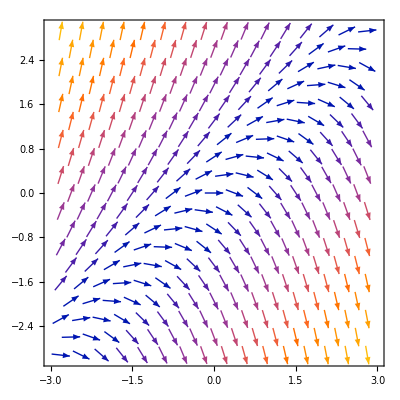

```mathematica
VectorPlot[{1, y - x}, {x, -3, 3}, {y, -3, 3}]
```

The current version of Mathematica (12) uses the color of the vectors to indicate magnitude, rather than length. In this context, we are concerned with only direction.  Mathematica controls the scale and style of these  vectors using the options VectorStyle and VectorScale. We can use these, for example, to remove the arrowheads. We also use the option Axes to display the coordinate axes. We will assign the variable slopefield to be the output from VectorPlot as we will want to use the plot again later.

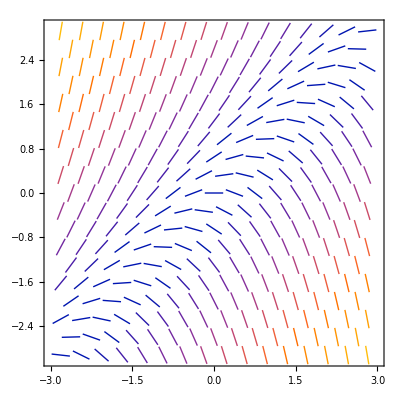

```mathematica
slopefield =  VectorPlot[{1,y-x},{x,-3,3},{y,-3,3}, 
	Axes->True,VectorStyle->Arrowheads[0]]
```

### Solving Differential Equations Symbolically

Mathematica has a built in function DSolve that will attempt to solve a differential equation symbolically. This function is extremely powerful and can handle a variety of different types of differential equations, including systems. Mathematica can also find numerical solutions using NDSolve, but we will focus on DSolve. Here’s how we can use DSolve to solve the differential equation ⅆy/ⅆx= y - x. Let’s assign j to be the output of this call to DSolve.

```mathematica
j = DSolve[y'[x]==y[x] -x, y, x]
```

{{y→Function[{x},1+x+ⅇ^x C[1]]}}

Here, c_1 represents an arbitrary constant. Notice that the output from DSolve is a rule which specifies the solution. This can be convenient if we would like to substitute our solution into other expressions. For example, the following code verifies that DSolve has indeed found a solution.

```mathematica
{y'[x] == y[x] - x}/.j
```

{{True}}

If you would like an expression instead of a rule, you can use DSolveValue.

```mathematica
DSolveValue[y'[x] == y[x] - x, y[x], x]
```

1+x+ⅇ^x C[1]

DSolve can also handle boundary conditions. Suppose we wish to find the solution that passes through the origin. We need only add this condition to the first argument of DSolve. Let’s assign f to be this function and fplot to be the plot of the solution in red (we’ll suppress the output for now).

```mathematica
f = DSolveValue[{y'[x] == y[x] - x, y[0]==0}, y[x], x]
fplot = Plot[f, {x, -3, 3}, PlotRange->{-3,3}, PlotStyle->Red];
```

1-ⅇ^x+x

We have now assigned fplot to be the plot of the solution and slopefield to be the plot of the
slope field for the differential equation. We can combine graphics by using the Show function.
Here is the solution and the slope field together.

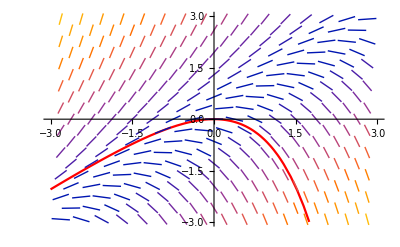

```mathematica
Show[fplot, slopefield]
```

## Exercises

### Exercise 1

Consider the initial value problem y' = y - x with y(0) = k.

Using Manipulate for −3 ≤ k ≤ 3, plot the solution to the initial value problem along
with the slope field for −3 ≤ x,y ≤ 3.
(Hint: If you attempt to do this in a single line using something like Plot[DSolve[...]]
you will get some error messages. This is because the plot command attempts to plug
in values for x into the DSolve command before solving the differential equation in the
variable x. You would like Mathematica to first solve the differential equation and then
later plug in values of x into the solution. This can be forced by using the function
Evaluate. Simply place the call to DSolve inside a a call to evaluate and Mathematica
will first evaluate this expression before plugging in values for x.)

For which k is the solution a linear function?

For which k does the solution satisfy lim_(x →∞) y = ∞ ?

For which k does the solution satisfy lim_(x → ∞) y = −∞?

### Exercise 2

Consider the initial value problem y'= -2x y^2 with y(0) = k.

. Plot the slope field associated with this differential equation for −3 ≤ x,y ≤ 3.

Solve the initial value problem for a general k.

Using Manipulate for −3 ≤ k ≤ 3, plot the solution to the initial value problem (in red) along with the slope field.

For which k is the solution a constant function?

For which k is the solution bounded?

### Exercise 3

Consider the differential equation y' = -x/(2y).

Plot the slope field associated with this differential equation for −5 ≤ x, y ≤ 5. Force
the ratio of height to width of this plot to be 1 using the option AspectRatio.

Using Manipulate for −5 ≤ k ≤ 5, plot y = k x^2 along with the slope field from (a).
Again, the aspect ratio should be 1.

What do you observe about the tangent lines to the curve and the lines in the slope
field?

Justify your observation in words using mathematics.

### Exercise 4

Solve the following differential equations using Mathematica. You have learned
to solve these differential equations by hand at some point in your past (Math 242 or 244).The technique used to solve these by hand is identified in parentheses.

y-x ⅆy/ⅆx=3-2 x^2 y' 	(separable)

y' = y^2 sin x, y(0) = 1 	(separable)

(sin x) y' - y cos x = sin 2x, y(π/2) = 2	(integrating factor)

y' + y/(x ln(x))= 9 x^2	(integrating factor)

x^2 y' = y^2 + 3 x y + x^2 	(change of variables)

2 x^2 y' + 4 x y = 3 sin x, y(2π) = 0	(exact)

(1 + x^2) y'' = - 2 x y, y(0) = 1, y'(0) = 2	(replace with a system of first order equations)

y'' - 2y' - 3y = 0 	(constant coefficient homogeneous linear differential equation)

y''' - y'' + y' - y = 0, y(0) = 0, y'(0) = 1, y''(0) = 2	(same as above)

y'' + y = 6 ⅇ^x 	(undetermined coefficients)

### Exercise 5

Imagine a mass hanging from a spring attached to the ceiling at point (0,2). At equilibrium,
the mass will located at the origin. The following initial value problem governs the position y
(measured downward from equilibrium) of the mass in this mass-spring system as a function
of t.

(ⅆ^2 y)/(ⅆ t^2) + 2 a ⅆy/ⅆt + y = 0, y(0) = y_0, y'(0) = v_0

The constant a in the equation above acts as a “damping” constant on the system.

Write a function called DrawSpring[y]that will render the spring and the mass (preferably rectangular) centered at position y. Remember, positive y is measured downward from equilibrium in this problem. Make it so that the viewing window will allow you to see the mass for −2 ≤ y ≤ 4. Also, include a horizontal line corresponding to the equilibrium position. Test your program using Manipulate for −2 ≤ y ≤ 4. Your output for DrawSpring[3] should look something like this, but feel
free to make it fancier. See this stackexchange post.

Solve the differential equation with a = 0, y_0 = 1, v_0 = 0 and visualize the system by using Animate with 0 ≤ t ≤ 30 along with your function DrawSpring. Animate is a lot like Manipulate but starts playing immediately; remember you can slow the rate of play by clicking the slower button (two down arrows.) How many times will the mass pass through equilibrium? In this situation, there is no damping.

Solve the differential equation with a = 1/10, y_0 = 1, v_0 = 0 and again visualize the system using Animate with 0 ≤ t ≤ 30. Also, plot the solution in the plane. How many times will the mass pass through equilibrium for 0 ≤ t ≤ ∞? In this situation, we say that the system is underdamped.

Solve the differential equation with a = 1, y_0 = 1, v_0 = −3 and again visualize the system using Animate with 0 ≤ t ≤ 5. Also, plot the solution in the plane. How many times will the mass pass through equilibrium for 0 ≤ t ≤ ∞? In this situation, we say that the system is critically damped.

Solve the differential equation with a = 2, y 0 = 1, v 0 = −2 and again visualize the
system using Animate with 0 ≤ t ≤ 10. Also, plot the solution in the plane. How
many times will the mass pass through equilibrium for 0 ≤ t ≤ ∞? In this situation,
we say that the system is overdamped.

### Exercise 6

Imagine a coupled mass-spring system without damping where a mass m_1 hangs on a spring from the ceiling at point (0,2) and a mass m_2 hangs on a spring connected to m_1 . For the sake of consistency, let’s assume that when at equilibrium both springs have length 2 so that the mass m_1 would be located at the origin and the mass m_2 would be located two units below m_1 . Hooke’s law yields the following system of differential equations which govern the positions x and y (measured downward from equilibrium from their respective positions at equilibrium) at time t.

(ⅆ^2 x)/(ⅆ t^2)  = -x + ( y - x)
 (ⅆ^2 y)/(ⅆ t^2)  = - ( y - x)

Write a function called DrawSprings[x ,y] that will render the springs and the masses (preferably rectangular) at their respective positions x and y described above. Again, include dashed horizontal lines which correspond to the equilibrium positions of the springs. Make it so that the viewing window will allow you to see the masses for −2 ≤ x,y ≤ 2. Test your program using Manipulate for −2 ≤ x,y ≤ y. Your output for DrawSprings[-1,1] should look something like this, but feel free to make it fancier:

Look up the syntax for using DSolve for systems and solve the system of differential equations with x(0) = 0, x' (0) = 2, y(0) = 0, y' (0 ) = 0 and visualize the system by using Animate with 0 ≤ t ≤ 30 along with your function DrawSprings. Also, plot both solutions in the plane on the same graph. Play with the initial conditions to see what other kinds of motion you can obtain.

### Exercise 7

One of the most important “functions” in the study of physical systems is the Dirac delta function, usually denoted . The Dirac delta function is not actually a function; it is a member of a class of objects called generalized functions or distributions. The Dirac function is defined to be the mathematical object satisfying some desired properties:

1. ,
2.

1. Compute the integral of .  Plot the result.

2. Define . Compute the integral . Explain why integrating  times the delta function is sometimes referred to as “point evaluation”.

3. The delta function can be used to model instantaneous impulses applied to physical systems. Use  your solution to Exercise 5 to solve the forced equation, where  measures the amplitude of an instantaneous impulse applied at time ,

(ⅆ^2 y)/(ⅆ t^2) + 2 a ⅆy/ⅆt + y = F δ_T(x), y(0) = y_0, y'(0) = v_0

for a = 1/10, y_0 = 1, v_0 = 0, F = 1.5, T = 15 , and again visualize the system using Animate with 0 ≤ t ≤ 30. Also, plot the solution in the plane.